# Analysing Customer Shopping Trends

## Data Source

Kaggle Dataset Link-  https://www.kaggle.com/datasets/zeesolver/consumer-behavior-and-shopping-habits-dataset

## Variable Definitions

1. Customer ID: A unique identifier for each customer
2. Age: The age of the customer
3. Gender: The gender of the customer
4. Item Purchased: The name of the item purchased by the customer
5. Category: The category to which the purchased item belongs (e.g., Clothing, Footwear)
6. Purchase Amount (USD): The amount spent on the purchase, in US dollars
7. Location: The geographical location or state of the customer
8. Size: The size of the purchased item
9. Color: The color of the purchased item
10. Season: The season during which the purchase was made (e.g., Winter, Spring)
11. Review Rating: A numerical rating given by the customer for the purchased item
12. Subscription Status: Indicates whether the customer is subscribed to the store’s services or not
13. Shipping Type: The type of shipping chosen for the delivery (e.g., Express, Free Shipping, Next Day Air)
14. Discount Applied: Indicates whether a discount was applied to the purchase
15. Promo Code Used: Indicates whether a promotional code was used during the purchase
16. Previous Purchases: The number of previous purchases made by the customer
17. Payment Method: The method of payment used by the customer (e.g., Venmo, Cash, Credit Card)
18. Frequency of Purchases: How often the customer makes purchases (e.g., Weekly, Fortnightly, Annually)

## Wrangle 1. Importing our Dataset and cleaning it

### 1.1 Importing the dataset and finding the dimensions

```mathematica
SetDirectory[NotebookDirectory[]];
df= Import["shopping_behavior_updated.csv","Dataset",HeaderLines->1];
Dimensions[df]
data=Import["shopping_behavior_updated.csv"]
```

{3900,18}

```mathematica
Times@@{3900,18}
```

70200

```mathematica
data=Import["shopping_behavior_updated.csv"];
headers=data[[1,All]]
asso=AssociationThread[Range[Length[headers]]->headers]
```

{Customer ID,Age,Gender,Item Purchased,Category,Purchase Amount (USD),Location,Size,Color,Season,Review Rating,Subscription Status,Shipping Type,Discount Applied,Promo Code Used,Previous Purchases,Payment Method,Frequency of Purchases}

<|1→Customer ID,2→Age,3→Gender,4→Item Purchased,5→Category,6→Purchase Amount (USD),7→Location,8→Size,9→Color,10→Season,11→Review Rating,12→Subscription Status,13→Shipping Type,14→Discount Applied,15→Promo Code Used,16→Previous Purchases,17→Payment Method,18→Frequency of Purchases|>

### 1.2 Finding and removing missing values

```mathematica
dfcl= DeleteMissing[df]
Dimensions[dfcl]
```

Dataset[<>]

{3900,18}

Dataset::nolpky: The original Dataset expression was not found.

### 1.3 Formatting the dataset

```mathematica
dfcl1=Dataset[dfcl,HeaderStyle->Bold,HeaderAlignment-> Center ,HeaderBackground->Yellow]
```

Dataset[<>]

## Explore & Analyze 2. Customer trends Analysis

Exploring top 5 states with the highest purchases reveals key consumer patterns. From pinpointing popular categories to gauging the impact of seasonality, this journey provides actionable insights for businesses. We will be using the Previous Purchases as an indicator for Customer Loyalty and Market Potential.

### 2.1 States having the highest previous purchases

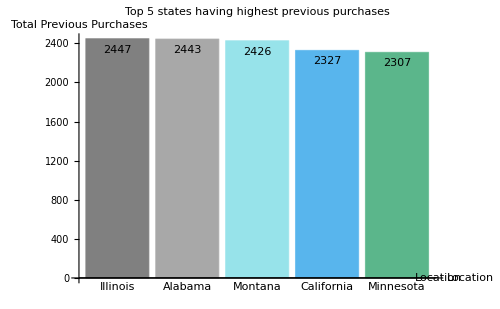

```mathematica
locationColumn="Location";
previousPurchasesColumn="Previous Purchases";
groupedData=dfcl1[GroupBy[locationColumn],Total,previousPurchasesColumn];
top5states=TakeLargestBy[groupedData,Total[#]&,5]
BarChart[top5states,
ScalingFunctions->None,
LabelingFunction->Top,
ChartLabels->Placed[{"Illinois","Alabama","Montana","California","Minnesota"},Below],
AxesLabel->{"Location","Total Previous Purchases"},
PlotLabel->"Top 5 states having highest previous purchases",
BarOrigin->Bottom,
AspectRatio->1/GoldenRatio,
Background->White,
ChartStyle->47,
ImageSize->500]
```

We deduce that the top 5 states having the highest market potential/ Customer Loyalty are Illinois, Alabama,Montana, California, Minnesota.

### 2.2 Popular Categories

Spotlight on the top categories driving consumer spending, guiding businesses in understanding market preferences.

#### 2.2.1 Overall Analysis of Popular Category Purchased

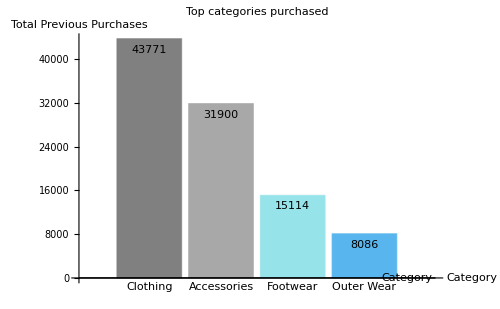

```mathematica
categoryColumn="Category";
previousPurchasesColumn="Previous Purchases";
groupedData1=dfcl1[GroupBy[categoryColumn],Total,previousPurchasesColumn];
topcategoriesoverall=TakeLargestBy[groupedData1,Total[#]&,4]
BarChart[topcategoriesoverall,
ScalingFunctions->None,
LabelingFunction->Top,
ChartLabels->Placed[{"Clothing","Accessories","Footwear","Outer Wear"},Below],
AxesLabel->{"Category","Total Previous Purchases"},
PlotLabel->"Top categories purchased",
BarOrigin->Bottom,
AspectRatio->1/GoldenRatio,
Background->White,
ChartStyle->47,
ImageSize->500]
```

We can observe that most total previous purchases are attributed to the clothing and accessories category and Outer Wear has the least number of total purchases.
Although this represents the population, lets go deeper and find out if this trend is extrapolated to the states having the highest previous purchases (found in 2.1)

#### 2.2.2 Most popular categories amongst the top 5 states having highest previous purchases

```mathematica
;
varLocation=Rest[filteredData[[All,7]]];
varCat= Rest[filteredData[[All,5]]];
varPreviousPurchases=ToExpression/@Rest[filteredData[[All,16]]];
data1=Transpose[{varLocation,varCat,varPreviousPurchases}];
ResourceFunction["CrossTabulate"][data1]
```

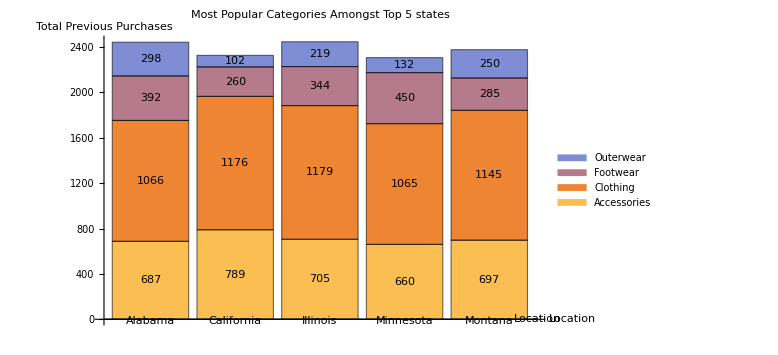

```mathematica
counts=Dataset[Association[
    "Alabama"->Association["Accessories"->687,"Clothing"->1066,"Footwear"->392,"Outerwear"->298],
    "California"->Association["Accessories"->789,"Clothing"->1176,"Footwear"->260,"Outerwear"->102],
    "Illinois"->Association["Accessories"->705,"Clothing"->1179,"Footwear"->344,"Outerwear"->219],
    "Minnesota"->Association["Accessories"->660,"Clothing"->1065,"Footwear"->450,"Outerwear"->132],
    "Montana"->Association["Accessories"->697,"Clothing"->1145,"Footwear"->285,"Outerwear"->250]
]];

categories={"Accessories","Clothing","Footwear","Outerwear"};

BarChart[Values/@counts,ChartLabels->Automatic,ChartLegends->categories,
  ChartLayout->"Stacked",ImageSize->Large,LabelingFunction->Center,
  ChartLabels->Placed[Placed[Round[Values@Flatten@counts,0.01],Center],Above],AxesLabel->{"Location","Total Previous Purchases"},
PlotLabel->"Most Popular Categories Amongst Top 5 states"]
```

We infer the following:
1. Clothing is the most bought category in amongst the states with the highest previous purchases. Illinois stands first, followed by California and Alabama.
2.  Accessories is the second most purchased category, with California in the first place and Alabama in the second.
3. Outer Wear is the least Purchased Category amongst these states
Therefore, the organization can focus on the supply chain and procurement sectors of the clothing and accessory categories since these categories are what customers are attracted to

### 2.3 Seasonal Dynamics:

Unraveling the influence of seasonality on individual categories, offering businesses cues to adapt to changing demands.

#### 2.3.1 Overall effect of Season on Previous Purchases

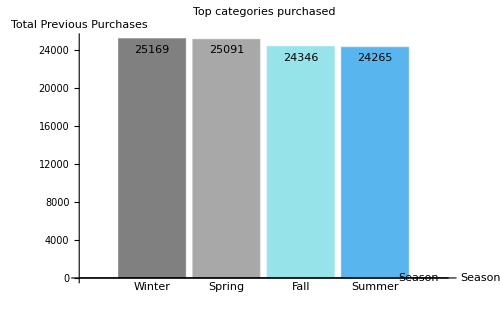

```mathematica
season="Season";
previousPurchases="Previous Purchases";
groupedData2=dfcl1[GroupBy[season],Total,previousPurchases];
seasonaleffect=TakeLargestBy[groupedData2,Total[#]&,4]
BarChart[seasonaleffect,
ScalingFunctions->None,
LabelingFunction->Top,
ChartLabels->Placed[{"Winter","Spring","Fall","Summer"},Below],
AxesLabel->{"Season","Total Previous Purchases"},
PlotLabel->"Top categories purchased",
BarOrigin->Bottom,
AspectRatio->1/GoldenRatio,
Background->White,
ChartStyle->47,
ImageSize->500]
```

The graph above shows that most of the total previous purchases are done in winter and the least are done in the summer season
This can be translated into building up the winter inventory through the other seasons to cater to the market requirements

#### 2.3.2 Effect of Seasonality on Previous Purchases of Categories in the states having highest previous purchases

```mathematica
varSeason= Rest[filteredData[[All,10]]];
data2=Transpose[{varCat,varSeason,varPreviousPurchases}];
ResourceFunction["CrossTabulate"][data2]
```

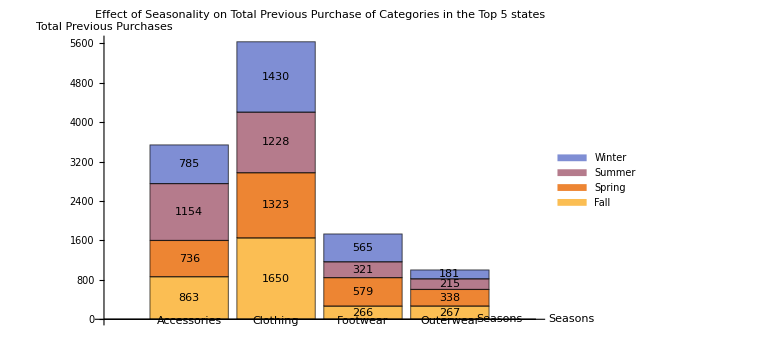

```mathematica
counts2=Dataset[Association["Accessories"->Association["Fall"->863,"Spring"->736,"Summer"->1154,"Winter"->785],
   "Clothing"->Association["Fall"->1650,"Spring"->1323,"Summer"->1228,"Winter"->1430],
   "Footwear"->Association["Fall"->266,"Spring"->579,"Summer"->321,"Winter"->565],
   "Outerwear"->Association["Fall"->267,"Spring"->338,"Summer"->215,"Winter"->181]]];
seasons={"Fall","Spring","Summer","Winter"};

BarChart[Values/@counts2,ChartLabels->Automatic,ChartLegends->seasons,
  ChartLayout->"Stacked",ImageSize->Large,LabelingFunction->Center,
  ChartLabels->Placed[Placed[Round[Values@Flatten@counts2,0.01],Center],Above],AxesLabel->{"Seasons","Total Previous Purchases"},
PlotLabel->"Effect of Seasonality on Total Previous Purchase of Categories in the Top 5 states"]
```

We can deduce the following:
1. Clothing seems to be the most purchased category during the fall season and least in the Summer Season
2. Accessories is purchased most in the Summer season and least in the least in the Spring Season
3. Footwear is purchased most during Spring Season and least in the Fall Season
4. Outerwear is, surprisingly, purchased most during the Spring Season and least in the Winter season.

In terms of popular category per season:
1. Clothing seems to be the most popular item purchased during Fall, Winter and Spring
2. Accessories seem to be the most purchased during Summer

For least popular category per season:
1. Footwear seems to be the least favorite category purchased in Fall
2. Outer wear is the least purchased during Spring and Summer and Winter

This gives the company more incentive to find out why Outer Wear is the least popular category until now and also focus on sustaining their popularity amongst their customers in the ‘Clothing Category’

### 2.4 Macro Insights:

Examining the broader impact of seasonality on total purchases, empowering businesses with a comprehensive understanding of market dynamics.

#### 2.4.1 Effect of Seasonality on Total Previous Purchases in the Top 5 States

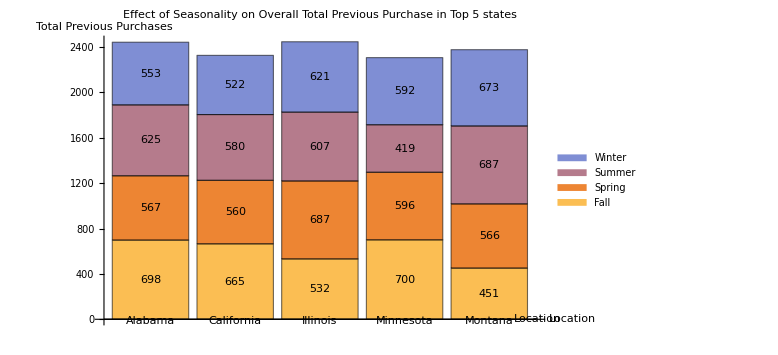

```mathematica
data3=Transpose[{varLocation,varSeason,varPreviousPurchases}];
table2= ResourceFunction["CrossTabulate"][data3]
seasons={"Fall","Spring","Summer","Winter"};
BarChart[Values/@table2,ChartLabels->Automatic,ChartLegends->seasons,
  ChartLayout->"Stacked",ImageSize->Large,LabelingFunction->Center,
  ChartLabels->Placed[Placed[Round[Values@Flatten@table2,0.01],Center],Above],AxesLabel->{"Location","Total Previous Purchases"},
PlotLabel->"Effect of Seasonality on Overall Total Previous Purchase in Top 5 states"]
```

We can observe that the previous purchases seem to be consistent throughout all the states in all the season. But most purchases are made in the Fall season and the least are made in the  Summer Season

#### 2.5 Categories Meet Payments: 2.5.1 Which is the most used payment method?

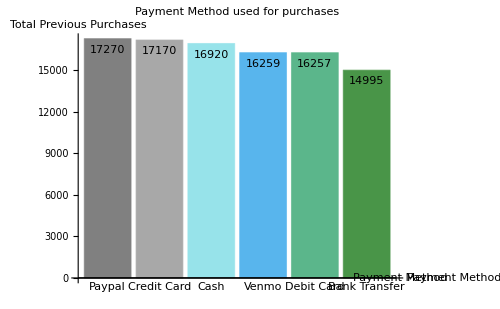

```mathematica
payment="Payment Method";
previousPurchases="Previous Purchases";
groupedData3=dfcl1[GroupBy[payment],Total,previousPurchases];
seasonaleffect=TakeLargestBy[groupedData3,Total[#]&,6]
BarChart[seasonaleffect,
ScalingFunctions->None,
LabelingFunction->Top,
ChartLabels->Placed[{"Paypal","Credit Card","Cash","Venmo","Debit Card","Bank Transfer"},Below],
AxesLabel->{"Payment Method","Total Previous Purchases"},
PlotLabel->"Payment Method used for purchases",
BarOrigin->Bottom,
AspectRatio->1/GoldenRatio,
Background->White,
ChartStyle->47,
ImageSize->500]
```

#### 2.5.2 Most purchased categories and payment methods for top 5 states

```mathematica
;
varLocation=Rest[filteredData[[All,7]]];
varPayment = Rest[filteredData[[All,17]]];
varCat= Rest[filteredData[[All,5]]];
varPreviousPurchases=ToExpression/@Rest[filteredData[[All,16]]];
data10=Transpose[{varPayment,varCat,varPreviousPurchases}];
table3= ResourceFunction["CrossTabulate"][data10]
(*sortedData=SortBy[table3,{-#[[1]]} &]*)
```

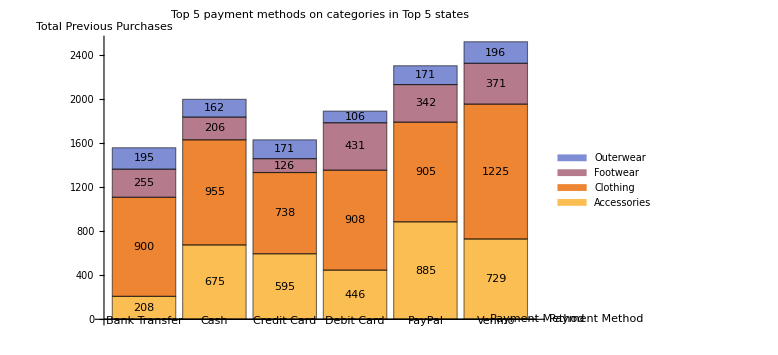

```mathematica
BarChart[Values/@table3,ChartLabels->Automatic,ChartLegends->categories,
  ChartLayout->"Stacked",ImageSize->Large,LabelingFunction->Center,
  ChartLabels->Placed[Placed[Round[Values@Flatten@table2,0.01],Center],Above],AxesLabel->{"Payment Method","Total Previous Purchases"},
PlotLabel->"Top 5 payment methods on categories in Top 5 states"]
```

## Conclusion

1. Clothing is consistently popular across seasons and payment methods.
2. Outerwear appears to be the least popular category across seasons, indicating a potential area for improvement or targeted marketing.
3. The company might want to investigate why Outerwear is least popular, especially during Winter when one might expect higher demand.
4. Payment method preferences vary across categories, suggesting that offering a variety of payment options might cater to different customer preferences.
5. Fall and Spring Season seem to be the busiest seasons for purchases